# Contour Plots of Triaxial Dark Matter Halos Potential

Ying Zhang

```mathematica
Motivation
```

Many mechanisms could potentially address the evolution and appearance of spiral structures within both gaseous and stellar disc galaxies, one of them is rotating triaxial dark matter halos. When I started to work on implementing analytical halos into gaseous disc galaxy in a Fortran-based SPH code, it was not only really hard for me to examine if my coding is right but also struggling to image the picture of the halo potential only according to the nasty equations.  Also, in previous studies, different researchers tend to choose different halo profiles in their running simulations. This could be confusing especially when their results differ with each other a little. For example, in ["Bekki et al."](https://iopscience.iop.org/article/10.1086/342262)[1],  they choose triaxial Navarro–Frenk–White profile(NFW) halo, but ["Khoperskov"](https://link.springer.com/article/10.1134%2FS1063772912010039) [2] turns to an another.  In my simulations, ["Khoperskov"](https://link.springer.com/article/10.1134%2FS1063772912010039) halo is adapted, in order to clarify a little, I also run this halo potential with the resolution and parameter profile in ["Bekki et al."](https://iopscience.iop.org/article/10.1086/342262)and make comparisons. Interestingly, we notice there is some slight difference between the two simulations. Showing the contour plots of those two potentials could help us understand this situation better.

-Graphics--Graphics-
The left-hand side [1] is clock-wise simulation result in Bekki et al. paper with triaxial NFW halo potential and the right-hand side is counter-clockwise with Khoperskov. The two shown pictures are taken at the same time point of the simulations. It is clear that the left one is more squeezed and compact than the right one - the pitch angle is smaller.

```mathematica
Khoperskov Triaxial Potential
```

Potential
The equation of the potential is: 
                                             ψ (x, y, z) = 4 π G ρ_0 a^2 × (ln ξ +  (arctan ξ)/ξ+ 1/2ln (1 + ξ^2)/ξ^2)
and          
                                                ξ = √(x^2/a^2 +y^2/b^2 + z^2/c^2)        
                                                ρ_0 = M_0/ [ 4 π a^3 ( R/a - ArcTan [ R/a ] ) ]
a, b and c are characteristic scales to describe the triaxiality of the dark matter halo,  ρ_0is the core density distribution of dark matter halo. First we set up the constants and in order to simplify a little, we only consider the the x-y plane and get rid of some constants that are of no significance such as gravitational constant G and halo mass M_h.

```mathematica
R = 12;
a = 6;
b = 0.8 a;
Subscript[ρ, h] = 1/(4Pi a^3(R/a - ArcTan[R/a]));
```

The triaxial dark matter halo also rotates, so we implement rotation of axis and the direction is clockwise, this means our potential is rotating with an angle described by θ.

```mathematica
x1[x_, y_, θ_]:= x * Cos[θ] - y * Sin[θ];
y1[x_, y_, θ_]:= y * Cos[θ] + x * Sin[θ];
```

which leads potential to be a function of position and the rotational angle.

```mathematica
ξ[x_, y_, θ_]:= Sqrt[x1[x, y, θ]^2/a^2 + y1[x, y,θ]^2/b^2];
ψ[x_, y_, θ_]:= 4 Pi * Subscript[ρ, h] * a^2 (Log[ξ[x,y,θ]]+ArcTan[ξ[x,y,θ]]/ξ[x,y,θ] + 1/2 Log[(1+ξ[x,y,θ]^2)/ξ[x,y,θ]^2]);
```

```mathematica
NFW Triaxial Potential
```

We do the same thing for Navarro–Frenk–White profile(NFW) potential.

Potential

The triaxial NFW potential is described as below :^[3]
                                                  ϕ( x, y, z)  =amp/(4  π a^3) 1/((m / a) (1+ m / a )^2)       
                                                  m^2 = x^2 + y^2/b^2 + z^2/c^2
Same as what we deal with the K halo, we only consider x-y plane and get rid of constant amp.

```mathematica
m[x_,y_,θ_]:=Sqrt[x1[x,y,θ]^2+y1[x,y,θ]^2/b^2];
ϕ[x_,y_,θ_]:=1/(4 π a^2 m[x,y,θ](1+m[x,y,θ]/a)^2);
```

Here we assume θ = 0 and then draw the contour plots of both to show the difference between those and suggest what might be happening in the previous simulations results shown above.

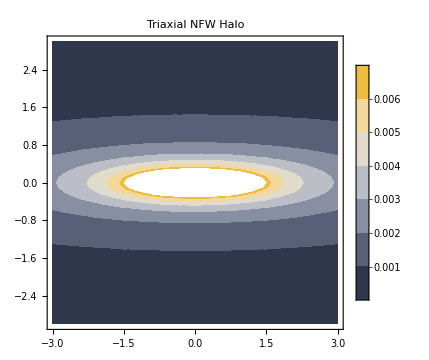
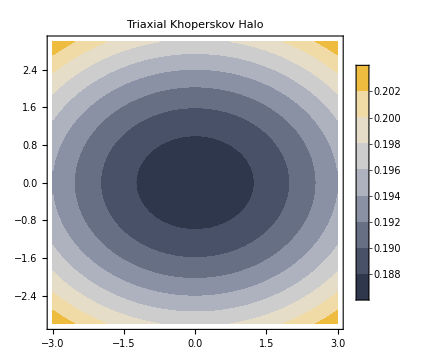

```mathematica
Row[ContourPlot[#⟦1⟧,{x,-3,3},{y,-3,3}, 
              Axes->True, ColorFunction->"GrayYellowTones", 
	             ContourLines->False, ImageSize->Medium,
                      PlotLegends->Automatic,PlotLabel->#⟦2⟧]&/@
                        {{ϕ[x, y, π/2],"Triaxial NFW Halo"},{ ψ[x, y, 0],"Triaxial Khoperskov Halo"}}]
```

The left side is NFW halo and the other one is K halo. We could see NFW is more oblate than K halo which could address why we observe the squeezed results in Bekki et al. paper regardless of their non-uniformed magnitude.

```mathematica
Manipulate the ContourPlot
```

Finally we could use Manipulate and ContourPlot function to demonstrate how the triaxial dark matter halo evolves with the change of the phase θ . Here we give the interactive function.

```mathematica
Manipulate[Row[ContourPlot[#⟦1⟧,{x,-3,3},{y,-3,3}, 
              Axes->True, ColorFunction->"GrayYellowTones", 
	             ContourLines->False, ImageSize->Medium,
                      PlotLegends->Automatic,PlotLabel->#⟦2⟧]&/@
                        {{ϕ[x, y, θ + π/2],"Triaxial NFW Halo"},{ ψ[x, y, θ],"Triaxial Khoperskov Halo"}}],
                           {{θ,Pi,"Phase"},Pi,π/16}]
```

```mathematica
Further Exploration
```

Other dark matter halo profiles are also adapted in the search of spiral arms within stellar discs like combining ["Hernquist halo"](https://academic.oup.com/mnras/article-abstract/461/3/2789/2608539?redirectedFrom=PDF) with two lower-order spherical harmonic terms [3]. We could also draw contour plots of this to investigate more.

```mathematica
Reference
```

[1] K. Bekki and K. C. Freeman, Astrophys. J. Vol. 56, No. 1, pp. 16 - 28 (2012)
[2] A. V. Khoperskov et al., Astronomy Reports, Vol. 56, N0. 1 (2012)
[3] S. Hu and D. Sijacki, MNARS 461, 2789 - 2808 (2016)

```mathematica
Author Contact Information
```

zhang@astro1.sci.hokudai.ac.jp